```mathematica
"ϕ==> Rotate"
"θ==> Tilt"
"ψ==>Twist"
"χ_(i, j, k)^(2)==>Laboratory Coordination, λ(x,y,z)"
"χ_(l, m, n)^(2)==>Molecular Coordination, η(a,b,c)"
```

```mathematica
"From C3V Character Table"
```

```mathematica
"β_(a, a, a)==E ⊗ E==A_1,   Asymmetric"
"β_(a, a, c)==A_1 ⊗ A_1==A_1,   Symmetric"
"β_(a, b, b)==E ⊗ E==A_1,   Asymmetric"
"β_(a, c, a)==E ⊗ E==A_1,   Asymmetric"
"β_(b, a, b)==E ⊗ E==A_1,   Asymmetric"
"β_(b, b, a)==E ⊗ E==A_1,   Asymmetric"
"β_(b, b, c)==A_1 ⊗ A_1==A_1,   Symmetric"
"β_(b, c, b)==E ⊗ E==A_1,   Asymmetric"
"β_(c, a, a)==E ⊗ E==A_1,   Asymmetric"
"β_(c, b, b)==E ⊗ E==A_1,   Asymmetric"
"β_(c, c, c)==A_1 ⊗ A_1==A_1,   Symmetric"
```

```mathematica
x=a=1
y=b=2
z=c=3
```

1

2

3

```mathematica
"Non-zero Microscopic Hyperpolarizability"
```

```mathematica
"Symmetric"
Subscript[β, b,b,c]=Subscript[β, a,a,c]
Subscript[β, c,c,c]
"Asymmetric"
Subscript[β, b,c,b]=Subscript[β, a,c,a]
Subscript[β, c,b,b]=Subscript[β, c,a,a]
Subscript[β, b,b,a]=Subscript[β, a,b,b]=Subscript[β, b,a,b]=-Subscript[β, a,a,a]
```

Symmetric

β_(1,1,3)

β_(3,3,3)

Asymmetric

β_(1,3,1)

β_(3,1,1)

-β_(1,1,1)

```mathematica
"Zero Microscopic Hyperpolarizability"
```

```mathematica
Subscript[β, a,a,b]=Subscript[β, a,b,a]=Subscript[β, a,b,c]=Subscript[β, a,c,b]=Subscript[β, a,c,c]=0
Subscript[β, b,a,a]=Subscript[β, b,a,c]=Subscript[β, b,b,b]=Subscript[β, b,c,a]=Subscript[β, b,c,c]=0
Subscript[β, c,a,b]=Subscript[β, c,a,c]=Subscript[β, c,b,a]=Subscript[β, c,b,c]=Subscript[β, c,c,a]=Subscript[β, c,c,b]=0
```

0

0

0

```mathematica
"Euler Transformation Matrix"
```

```mathematica
ℝ=({{Cos[ψ]Cos[ϕ]-Cos[θ]Sin[ϕ]Sin[ψ], -Sin[ψ]Cos[ϕ]-Cos[θ]Sin[ϕ]Cos[ψ], Sin[θ]Sin[ϕ]}, {Cos[ψ]Sin[ϕ]+Cos[θ]Cos[ϕ]Sin[ψ], -Sin[ψ]Sin[ϕ]+Cos[θ]Cos[ϕ]Cos[ψ], -Sin[θ]Cos[ϕ]}, {Sin[θ]Sin[ψ], Sin[θ]Cos[ψ], Cos[θ]}})
```

{{Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ],Sin[θ] Sin[ϕ]},{Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[ϕ] Sin[θ]},{Sin[θ] Sin[ψ],Cos[ψ] Sin[θ],Cos[θ]}}

```mathematica
"For SPS"
```

```mathematica
Subscript[χ, i, j, k]=∑_(l=a)^c ∑_(m=a)^c ∑_(n=a)^c   ℝ[[i,l]] ℝ[[j,m]] ℝ[[k,n]] Subscript[β, l ,m ,n]/.{i->y,j->z,k->y}
```

Part::pspec: Part specification i is neither an integer nor a list of integers.

Part::pspec: Part specification j is neither an integer nor a list of integers.

Part::pspec: Part specification k is neither an integer nor a list of integers.

General::stop: Further output of Part will be suppressed during this calculation.

Sin[θ] Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 β_(1,1,1)-2 Cos[ψ] Sin[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) β_(1,1,1)-Sin[θ] Sin[ψ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 β_(1,1,1)-Cos[ϕ] Sin[θ]^2 Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) β_(1,1,3)-Cos[ϕ] Cos[ψ] Sin[θ]^2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) β_(1,1,3)+Cos[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 β_(1,3,1)+Cos[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 β_(1,3,1)-Cos[ϕ] Sin[θ]^2 Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) β_(3,1,1)-Cos[ϕ] Cos[ψ] Sin[θ]^2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) β_(3,1,1)+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 β_(3,3,3)

```mathematica
"SPS Symmetric Stretching-->β_(a, a, c) , β_(c, c, c)"
```

```mathematica
Subscript[χ, y,z,y]^((2)ss)=
Expand[-Cos[ϕ] Sin[θ]^2 Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) Subscript[β, a,a,c]-Cos[ϕ] Cos[ψ] Sin[θ]^2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) Subscript[β, a,a,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]]

=-Cos[θ] Cos[ϕ]^2 Cos[ψ]^2 Sin[θ]^2 Subscript[β, a,a,c]-Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ψ]^2 Subscript[β, a,a,c]+Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Subscript[β, c,c,c]
```

```mathematica
R=Subscript[β, a,a,c]/Subscript[β, c,c,c]

Subscript[χ, y,z,y]^((2)ss)=Subscript[β, c,c,c](-Cos[θ] Cos[ϕ]^2 Cos[ψ]^2 Sin[θ]^2 R-Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ψ]^2 R+Cos[θ] Cos[ϕ]^2 Sin[θ]^2)
```

```mathematica
"Average Over Orientation (ϕ,ψ)"
```

```mathematica
Subscript[Ν, s]/(2π)^2(∫_0^(2π) ∫_0^(2π) (Subscript[β, c,c,c](-Cos[θ] Cos[ϕ]^2 Cos[ψ]^2 Sin[θ]^2 R-Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ψ]^2 R+Cos[θ] Cos[ϕ]^2 Sin[θ]^2))ⅆϕⅆψ)

=-1/2 (-1+R) Cos[θ] Sin[θ]^2 Subscript[Ν, s] Subscript[β, c,c,c]
```

```mathematica
Subscript[χ, y,z,y]^((2)ss)=1/2 Subscript[Ν, s] Subscript[β, c,c,c](1-R)(Cos[θ]-Cos[θ]^3)
```

Set::write: Tag Power in χ_2, 2, 3 2 s^2 is Protected.

1/2 (3 Cos[θ]+Cos[θ]^3)

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, c,c,c]=1
R=2
```

1

1

2

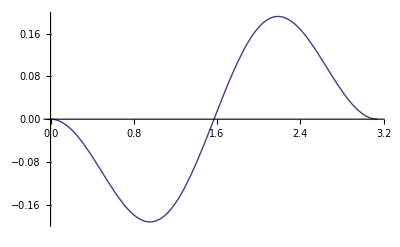

```mathematica
Plot[1/2 Subscript[Ν, s] Subscript[β, c,c,c](1-R)(Cos[θ]-Cos[θ]^3),{θ,0Degree, 180 Degree}]
```

```mathematica
"SPS Asymmetric Stretching-->β_(a, c, a) , β_(c, a, a) , β_(a, a, a)"
```

```mathematica
Subscript[χ, y,z,y]^((2)as)=
Expand[Sin[θ] Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 Subscript[β, a,a,a]-2 Cos[ψ] Sin[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) Subscript[β, a,a,a]-Sin[θ] Sin[ψ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 Subscript[β, a,a,a]+Cos[θ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ])^2 Subscript[β, a,c,a]+Cos[θ] (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ])^2 Subscript[β, a,c,a]-Cos[ϕ] Sin[θ]^2 Sin[ψ] (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) Subscript[β, c,a,a]-Cos[ϕ] Cos[ψ] Sin[θ]^2 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) Subscript[β, c,a,a]]

=-2 Cos[θ] Cos[ϕ] Cos[ψ]^3 Sin[θ] Sin[ϕ] Subscript[β, a,a,a]-3 Cos[θ]^2 Cos[ϕ]^2 Cos[ψ]^2 Sin[θ] Sin[ψ] Subscript[β, a,a,a]+3 Cos[ψ]^2 Sin[θ] Sin[ϕ]^2 Sin[ψ] Subscript[β, a,a,a]+6 Cos[θ] Cos[ϕ] Cos[ψ] Sin[θ] Sin[ϕ] Sin[ψ]^2 Subscript[β, a,a,a]+Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ψ]^3 Subscript[β, a,a,a]-Sin[θ] Sin[ϕ]^2 Sin[ψ]^3 Subscript[β, a,a,a]+Cos[θ]^3 Cos[ϕ]^2 Cos[ψ]^2 Subscript[β, a,c,a]+Cos[θ] Cos[ψ]^2 Sin[ϕ]^2 Subscript[β, a,c,a]+Cos[θ]^3 Cos[ϕ]^2 Sin[ψ]^2 Subscript[β, a,c,a]+Cos[θ] Sin[ϕ]^2 Sin[ψ]^2 Subscript[β, a,c,a]-Cos[θ] Cos[ϕ]^2 Cos[ψ]^2 Sin[θ]^2 Subscript[β, c,a,a]-Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ψ]^2 Subscript[β, c,a,a]
```

```mathematica
"Average Over Orientation (ϕ,ψ)"
```

```mathematica
Subscript[Ν, s]/(2π)^2(∫_0^(2π) ∫_0^(2π) (-2 Cos[θ] Cos[ϕ] Cos[ψ]^3 Sin[θ] Sin[ϕ] Subscript[β, a,a,a]-3 Cos[θ]^2 Cos[ϕ]^2 Cos[ψ]^2 Sin[θ] Sin[ψ] Subscript[β, a,a,a]+3 Cos[ψ]^2 Sin[θ] Sin[ϕ]^2 Sin[ψ] Subscript[β, a,a,a]+6 Cos[θ] Cos[ϕ] Cos[ψ] Sin[θ] Sin[ϕ] Sin[ψ]^2 Subscript[β, a,a,a]+Cos[θ]^2 Cos[ϕ]^2 Sin[θ] Sin[ψ]^3 Subscript[β, a,a,a]-Sin[θ] Sin[ϕ]^2 Sin[ψ]^3 Subscript[β, a,a,a]+Cos[θ]^3 Cos[ϕ]^2 Cos[ψ]^2 Subscript[β, a,c,a]+Cos[θ] Cos[ψ]^2 Sin[ϕ]^2 Subscript[β, a,c,a]+Cos[θ]^3 Cos[ϕ]^2 Sin[ψ]^2 Subscript[β, a,c,a]+Cos[θ] Sin[ϕ]^2 Sin[ψ]^2 Subscript[β, a,c,a]-Cos[θ] Cos[ϕ]^2 Cos[ψ]^2 Sin[θ]^2 Subscript[β, c,a,a]-Cos[θ] Cos[ϕ]^2 Sin[θ]^2 Sin[ψ]^2 Subscript[β, c,a,a])ⅆϕⅆψ)

=1/4 Cos[θ] Subscript[Ν, s] ((3+Cos[2 θ]) Subscript[β, a,c,a]-2 Sin[θ]^2 Subscript[β, c,a,a])
```

```mathematica
"Isotropic Interface--> β_(c, a, a)=β_(a, c, a)"
```

```mathematica
Subscript[β, c,a,a]=Subscript[β, a,c,a]
```

β_(a,c,a)

```mathematica
Simplify[1/4 Cos[θ] Subscript[Ν, s] ((3+Cos[2 θ]) Subscript[β, a,c,a]-2 Sin[θ]^2 Subscript[β, c,a,a])]

=Cos[θ]^3 Subscript[Ν, s] Subscript[β, a,c,a]
```

Cos[θ]^3 Ν_s β_(a,c,a)

```mathematica
Subscript[χ, y,z,y]^((2)as)=Subscript[Ν, s] Subscript[β, a,c,a] Cos[θ]^3
```

```mathematica
"Plot"
```

```mathematica
Subscript[Ν, s]=1
Subscript[β, a,c,a]=1
```

1

1

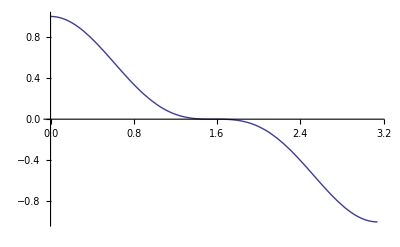

```mathematica
Plot[Subscript[Ν, s] Subscript[β, a,c,a] Cos[θ]^3,{θ,0Degree, 180 Degree}]
```